# Deep neural networks for regression

## Content

Introduction

Data

Importing

Examining

Splitting

Normalizing

Preparing

Model

Creating

Initializing

Training

Testing the model

Predict[] function

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Introduction

In regression problems, the target variable is of numerical type.  This distinguishes it from a classification problem, where the target variable is categorical in nature.

Regression problems require specific loss functions and a different output layer of a densely connected neural network.  In this tutorial we will take a look at a how to import data from a spreadsheet file, how to split it into a training and a test set, how to normalize it, and how to format it for use in a Wolfram Language neural network.

At the end of this tutorial, we will also take a look at the built-in Predict[] function.

## Data

### Import

The data is in the form of a comma separated values file.  The file contain no column header row, making it ideal for import.  The file is in the same folder as this notebook on my internal drive, so is referred to directly in the Import[] function.  This is possible with the use of the SetDirectory[NotebookDirectory[]] functions at the start of this notebook.

```mathematica
dataSet=Import["RegressionData.csv"];
```

### Examining

The first five samples are shown below in table form (using the suffix, //, notation for the TableForm[] function).

```mathematica
dataSet⟦;;5⟧//TableForm
```

5.8 | 0.24 | 0.28 | 1.4 | 0.038 | 40 | 0.98711 | 3.1 | 0.29 | 13.9 | 6.7
4.9 | 0.33 | 0.31 | 1.2 | 0.016 | 39 | 0.98713 | 3.33 | 0.59 | 14 | 7.6
4.7 | 0.67 | 0.09 | 1 | 0.02 | 5 | 0.98722 | 3.3 | 0.34 | 13.6 | 5
5 | 0.61 | 0.12 | 1.3 | 0.009 | 65 | 0.9874 | 3.26 | 0.37 | 13.5 | 5.3
5.4 | 0.3 | 0.3 | 1.2 | 0.029 | 25 | 0.98742 | 3.31 | 0.4 | 13.6 | 7.1

The Dimensions[] function allows us to to look at the number of samples and the number of feature variables plus target variable.

```mathematica
Dimensions[dataSet]
```

{4898,11}

We note that there are 4898 samples, 10 feature variable and a target variable.  In the code below, we use the Table[] function to iterate over all the variables in order to create a histogram for each.

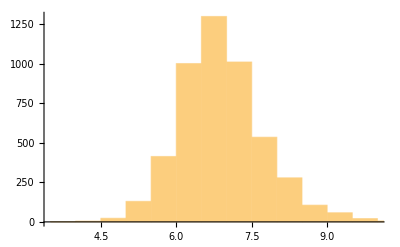
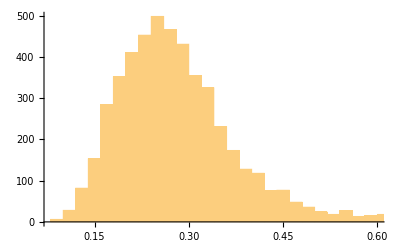
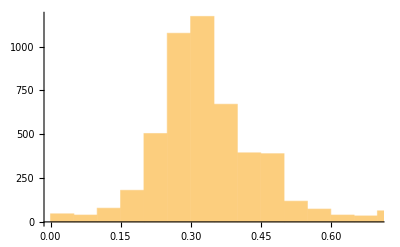
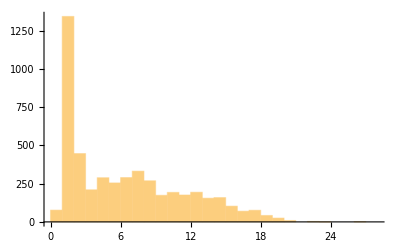
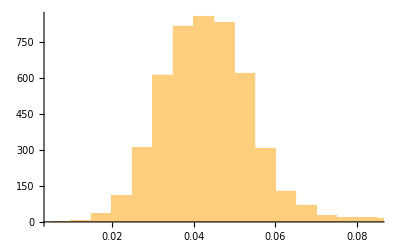
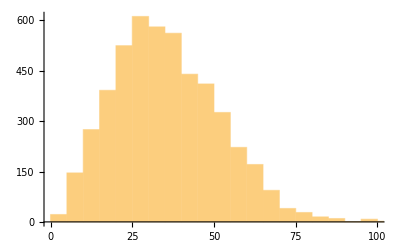
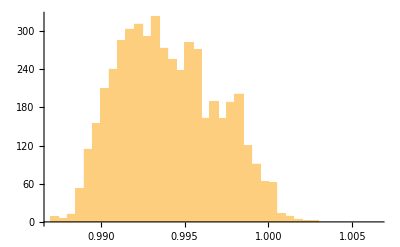
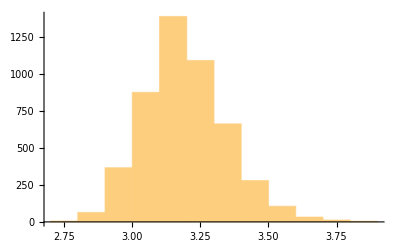

```mathematica
Table[Histogram[dataSet⟦;;,i⟧],{i,11}]
```

### Splitting

Since this is a very small dataset, we will sample 20% as the test set.  This is using the TakeDrop[] function.

```mathematica
(*Creating an object, trainN, to hold an integer value representing 80% of the data*)
n=Length[dataSet];
trainN=Floor[0.8 n];
```

The code below takes an 80:20 random split of the data.  It stores the former into the dataTrain object and the latter into the dataTest object.  We also take a look at the dimensions of the two new datasets.

```mathematica
RandomSeed[123];
{dataTrain,dataTest}=TakeDrop[RandomSample@dataSet,trainN];
Dimensions[dataTrain]
Dimensions[dataTest]
```

{3918,11}

{980,11}

In the code below we use indexing to separate out the feature and the target variables.  This leaves us with four objects: xTrain for the feature variable of the training set, yTrain for the target variable of the training set, xTest for the feature variables of the test set, and yTest for the target variable of the test set.

```mathematica
xTrain=dataTrain⟦All,1;;10⟧;
yTrain=dataTrain⟦All,11⟧;
xTest=dataTest⟦All,1;;10⟧;
yTest=dataTest⟦All,11⟧;
```

### Normalizing

The feature variable require normalization in order to help the gradient descent algorithm.  Normalizing is a generic term.  In the code below we actually standardize the data as shown in equation (1).

(x_i-x̄)/σ

The Standardize[] function is mapped onto the xTrain object, which has to be transposed, since the function runs across rows.  The result is transposed again to regain the original dimensions.  The 10 means and standard deviations are shown.  Rounding errors produce the means that are actually 0.

```mathematica
xTrainStandardized=Transpose@Map[Standardize,Transpose[xTrain]];
Mean[xTrainStandardized]
StandardDeviation[xTrainStandardized]
```

{7.75966×10^-16,6.27122×10^-17,1.46641×10^-17,1.43043×10^-16,1.04448×10^-16,1.60214×10^-16,1.40549×10^-14,-1.11736×10^-15,-6.42558×10^-16,1.50555×10^-15}

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

The Table[] function is used to iterate over each data point value in the test set of feature variables.  Remember that we use the training set’s original means and standard deviations and apply it to the test set values.

The code below also shows the 10 means and standard deviations of the normalized test features.  Because we used the values from the training set, they will not all be zeros and ones.

```mathematica
xTestStandardized=Transpose@Table[(xTest[[All,i]]-Mean[xTrain][[i]])/StandardDeviation[xTrain][[i]],{i,10}];
Mean[xTestStandardized]//N
StandardDeviation[xTestStandardized]//N
```

{0.00723251,0.0748543,0.0444364,-0.0258291,0.0385853,0.00617947,-0.0184247,-0.0502319,0.0328235,-0.000475439}

{0.975704,1.09885,1.02729,0.971445,1.08754,0.927088,0.978893,0.995089,0.994124,1.03967}

### Preparing

The network model that we are going to create requires the data to be in a specific format.  The code below achieves this by iterating over each corresponding row in the feature and target sets for both the training and test data.  The format must be a nested list, where each nested list is represented as {x_1,x_2,…,x_n→y_i}.

```mathematica
train=Table[xTrainStandardized⟦i,All⟧->yTrain⟦i⟧,{i,trainN}];
Dimensions[train]
train⟦;;1⟧ //N (*Show first sample*)
```

{3918}

{{-1.83196,1.55202,-1.85395,-1.04248,-0.773875,-1.6975,-1.09147,2.11875,-0.079611,0.561563}→4.}

```mathematica
test=Table[xTestStandardized⟦i,All⟧->yTest⟦i⟧,{i,Length[yTest]}];
Dimensions[test]
test⟦;;1⟧//N
```

{980}

{{-0.77068,4.89432,-2.68486,-0.630801,-0.214672,-1.00196,-1.25793,0.0675852,3.94624,2.60922}→6.9}

## Model

### Creating

We will once again use the chain form for creation of the network.  The code below creates three hidden layers using syntactic shortcuts.  Each hidden consists of 20 nodes and each uses the rectified linear unit activation function (relu).  The output layer has a single unit, which is specified as a “Scalar”.  Note that it has no activation function since this is a regression problem.  The “Input” argument is set to the number of feature variables.

```mathematica
net=NetChain[{20,Ramp,20,Ramp,20,Ramp,1},"Input"->10,"Output"->"Scalar"]
```

NetChain[<>]

### Initializing

The network weights and biases are now initialized.  The biases are set to zero and the weights are initialized with the “Random” method.  The suboption for “Random”is chosen to be “Weights” which allows for the stipulation of a distribution.  The 0.01 is in fact shorthand for a normal distribution with a mean of 0 and a standard deviation of 0.01.

```mathematica
net=NetInitialize[net,Method->{"Random","Weights"->0.01,"Biases"->0}]
```

NetChain[<>]

A histogram shows the distribution of the initial weight values.

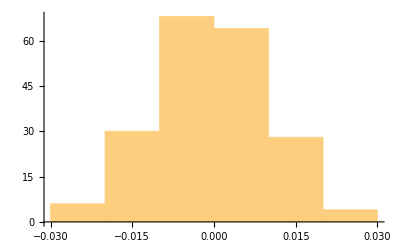

```mathematica
Histogram[Flatten[NetExtract[net,{1,"Weights"}]],{0.01}]
```

### Training

An object named trained is now created to train the model.  The mini-batch size is set to 32.  The optimizer used is “RMSProp” and the number of epochs is set to 25.  Note the use of the MeanAbsoluteLossLayer[] used as the loss function.  An alternative would be MeanSquaredLossLayer[].

```mathematica
trained=NetTrain[net,train,LossFunction->MeanAbsoluteLossLayer[],BatchSize->32,TargetDevice->"GPU",Method->"RMSProp",MaxTrainingRounds->25]
```

NetChain[<>]

## Testing the model

When using a classification model, the ClassifierMeasurements[] functions allowed us to created an object with properties for us to investigate.  At the time of creation of this tutorial, the PredictorMeasurements[] function only works with a predictor function created using the Predict[] function (see below).

We can calculate the mean absolute error manually, though.  Doing this will also allow us to create a comparison plot (scatter plot of actual and predicted values).

The code below creates an object called predicted which passes all the standardized training samples to our trained model.

```mathematica
predicted=trained[xTestStandardized];
```

Next up, we create another object that uses the Table[] function to create nested pairs of actual and predicted values.

```mathematica
actualPredicted=Table[{yTest⟦i⟧,predicted⟦i⟧},{i,Length[yTest]}];
```

We can take a quick look at the first pair.

```mathematica
{yTest⟦1⟧,predicted⟦1⟧}
```

{6.9,5.43198}

Below is a list plot showing the pairs as markers on a scatter plot (called a comparison plot).

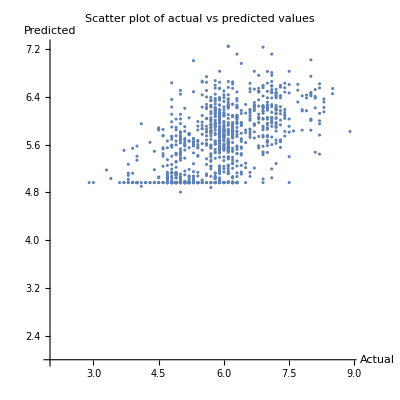

```mathematica
ListPlot[actualPredicted,PlotLabel->"Scatter plot of actual vs predicted values",AxesOrigin->{2,2},AspectRatio->1,AxesLabel->{"Actual","Predicted"}]
```

To calculate the mean absolute error requires the absolute values of the differences between the values in each pair.  In order to do this, we iterate again, but this time multiply the second value in each pair by negative one.

```mathematica
actualNegativePredicted=Table[{yTest⟦i⟧,-predicted⟦i⟧},{i,Length[yTest]}];
```

The nested list of Wolfram Language function below calculates the mean of the absolute value of all the differences.  The differences are calculated by adding the values of each pair.  By having multiplied the second value by negative one, it is in fact a subtraction.  The three @ symbols perform the Plus[] function on each pair.

```mathematica
Mean[Abs[Plus@@@actualNegativePredicted]]
```

0.628038

## Predict[] function

The Predict[] function automates machine learning.  In the code below we simply pass the formatted training data.  Only one argument is set to a non-default value and that is the performance goal.  Mathematica will look at different algorithms and produce a trained model.

```mathematica
p1=Predict[train,PerformanceGoal->"Quality"]
```

PredictorFunction[…]

This model can now be passed to the PredictorMeasurements[] function along with the formatted test data.

```mathematica
c1=PredictorMeasurements[p1,test]
```

PredictorMeasurementsObject[…]

All the properties of this object are listed below.

```mathematica
c1["Properties"]
```

{BatchEvaluationTime,BestPredictedExamples,ComparisonPlot,EvaluationTime,Examples,GeometricMeanProbabilityDensity,LeastCertainExamples,Likelihood,LogLikelihood,MeanCrossEntropy,MeanDeviation,MeanSquare,MostCertainExamples,Perplexity,PredictorFunction,ProbabilityDensities,ProbabilityDensityHistogram,Properties,RejectionRate,Report,ResidualHistogram,ResidualPlot,Residuals,StandardDeviation,StandardDeviationBaseline,TotalSquare,WorstPredictedExamples}

Let’s have a look at the comparison plot.

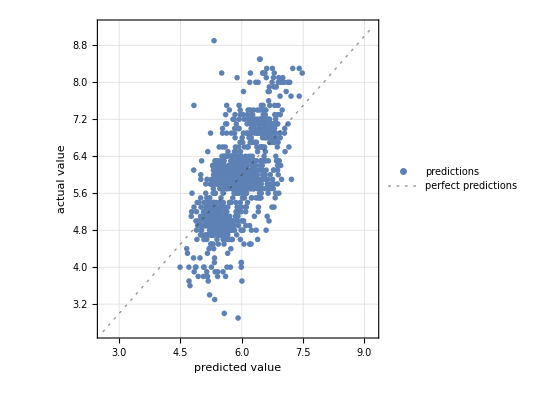

```mathematica
c1["ComparisonPlot"]
```

We can also take a look at the mean squared error.

```mathematica
c1["MeanSquare"]
```

0.523068

In the code below, we actually specify a generic neural network as machine learning type and then we have a look at the same properties.  The Predict[] function is a quick way of creating a regression model and automates the process of machine learning for you.  Remember that there is also a Classify[] function for classification automation.

```mathematica
p2=Predict[train,PerformanceGoal->"Quality",Method->"NeuralNetwork",TargetDevice->"GPU"]
```

```mathematica
c2=PredictorMeasurements[p2,test]
```

```mathematica
c2["ComparisonPlot"]
```